```mathematica
banana=x1^2/100+(x2+b x1^2-100 b)^2
b=0.05
phi[x_,y_] = {x,y + b*x^2 - 100*b};
phiI[x_,y_] = {x,y - b*x^2 + 100*b};
```

Notice that phi has unit Jacobian so that the density of phi(X) is simply pdf(phiInverse(x)) where pdf is the pdf of X, see http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.52.3205&rep=rep1&type=pdf

```mathematica
randn[]:=RandomVariate[NormalDistribution[0,40]]
```

```mathematica
list=Table[phiI[randn[],randn[]],{i,100000}]
Histogram3D[list]
```

{{15.1304,-26.7889},{-18.4466,-64.8763},{-81.3963,-303.857},{67.61,-176.815},99993,{-54.5252,-155.577},{-7.1767,-67.7666},{32.7927,-68.0075}}
 |  |  |  |

-Graphics3D-

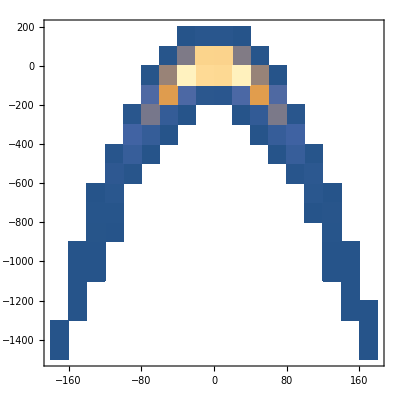

```mathematica
DensityHistogram[list,Automatic]
```